```mathematica
dataPath = "../data/2017/MessexperimentGeschwindigkeitenSS2017.csv";
data= SemanticImport@FileNameJoin@{NotebookDirectory[],dataPath};
```

```mathematica
längeEbene = 33 ;
längeTreppe = 20;
```

```mathematica
dataAuf = data[Select[#Treppe == "auf"&], <|
"id"->"ID Proband", 
"runde"->"Runde",
"bemerkung"-> "Bemerkung",
 "vAuf"->(längeTreppe/#"Zeit in sec"&)
|>];
dataAb = data[Select[#Treppe == "ab"&], <|
"id"->"ID Proband", 
"runde"->"Runde",
"bemerkung"-> "Bemerkung",
 "vAb"->(längeTreppe/#"Zeit in sec"&)
|>];
dataEbene = data[Select[#Ebene == "x"&], <|
"id"->"ID Proband", 
"runde"->"Runde",
"bemerkung"-> "Bemerkung",
 "vEbene"->(längeEbene/#"Zeit in sec"&)
|>];

abauf = JoinAcross[dataAuf, dataAb, {"id","runde"}];
gesamt = JoinAcross[abauf,dataEbene, {"id","runde"}];
```

```mathematica
a = Normal@Values@gesamt[Select[#bemerkung==""&],{"vAuf","vEbene"}];
gesamt[Select[#bemerkung!=""&]]
```

Dataset[<>]

FittedModel[0.538987+0.720221 x]

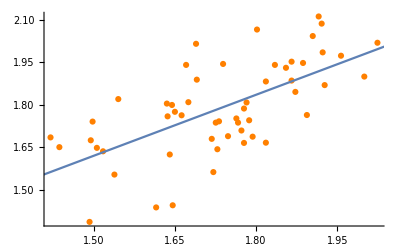

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.596316 | 0.596316 | 36.6727 | 1.57165×10^-7
Error | 52 | 0.845545 | 0.0162605 |  | 
Total | 53 | 1.44186 |  |  |

```mathematica
lm = LinearModelFit[a,{x},{x}]
Show[ListPlot[lm["Data"],PlotStyle->Orange],Plot[lm[x],{x,0,100}]]
lm["ANOVATable"]
```